```mathematica
SetDirectory["..."];
```

```mathematica
f1data=Import["Data_Figure_1.csv"];
```

Figures

```mathematica
f1data[[1;;15]]//MatrixForm
```

(Rank | ISO3 | Country | EU | Sink_wo_OS |  | Sink_w_OS |  | OverseaGain | 
 |  |  |  | Mean | Std | Mean | Std | Mean | Std
 |  |  |  | MtCO2 | MtCO2 | MtCO2 |  |  | 
1 | EU |  |  | 201.066 | 8.23865 | 548.69 | 23.6411 | 347.623 | 22.1591
2 | USA |  |  | 248.501 | 9.9328 | 429.092 | 20.5008 | 180.591 | 13.1717
3 | AUS |  |  | 194.267 | 27.7525 | 254.18 | 27.7525 | 59.9127 | 3.85712
4 | FRA |  |  | 9.83204 | 1.40458 | 252.693 | 1.40458 | 242.861 | 19.8503
5 | GBR |  |  | 20.9085 | 2.98692 | 230.341 | 2.98692 | 209.432 | 9.19475
6 | RUS |  |  | 222.927 | 0.862218 | 222.927 | 30.9965 | 0 | 0
7 | IDN |  |  | 170.211 | 24.3159 | 170.211 | 24.3159 | 0 | 0
8 | CAN |  |  | 162.992 | 23.2846 | 162.992 | 23.2846 | 0 | 0
9 | NZL |  |  | 116.037 | 16.5767 | 125.101 | 16.5767 | 9.06386 | 1.29484
10 | JPN |  |  | 114.961 | 16.423 | 117.047 | 16.423 | 2.08589 | 0.297985
11 | KIR |  |  | 97.2495 | 4.2537 | 97.2495 | 8.43129 | 0 | 0
12 | CHL |  |  | 70.3397 | 10.0485 | 90.9706 | 10.0485 | 20.631 | 2.94728)

```mathematica
eezsink=Table[0,{i,11},{j,3}];
eezsink[[1]]={"country","eez","oversea"};
eezsink[[2;;,1]]=f1data[[{4,5,6,8,9,10,11,12,13,14},2]];
Do[eezsink[[i,2]]=Around[f1data[[i+2,5]],f1data[[i+2,6]]],{i,2,4}]
Do[eezsink[[i,2]]=Around[f1data[[i+3,5]],f1data[[i+3,6]]],{i,5,11}]
Do[eezsink[[i,3]]=Around[f1data[[i+2,9]],f1data[[i+2,10]]],{i,2,4}]
Do[eezsink[[i,3]]=Around[f1data[[i+3,9]],f1data[[i+3,10]]],{i,5,11}]
```

```mathematica
eezsink//MatrixForm
```

(country | eez | oversea
EU | 201.8. | 348.22.
USA | 249.10. | 181.13.
AUS | 194.28. | 60.4.
GBR | 20.93.0 | 209.9.
RUS | 222.90.9 | 0
IDN | 170.24. | 0
CAN | 163.23. | 0
NZL | 116.17. | 9.11.3
JPN | 115.16. | 2.090.30
KIR | 97.4. | 0)

```mathematica
f1L=SwatchLegend[{Lighter[Gray,0.7], Lighter[Green,0.7]},{Style["domestic",20],Style["oversea territories",20]},LegendLayout->{"Column",1}]
```

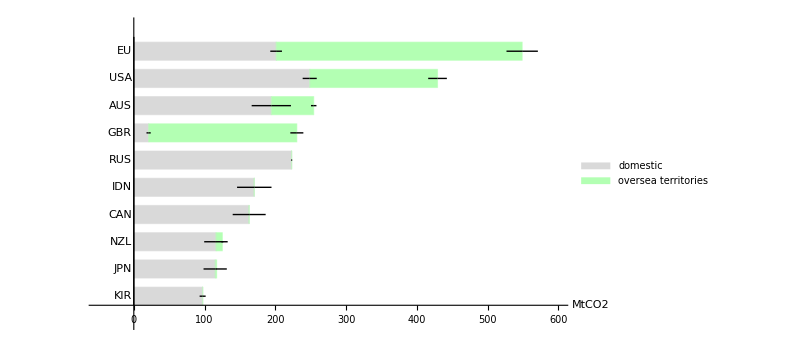

```mathematica
f1=Legended[BarChart[Reverse[eezsink[[2;;11,{2,3}]]],ChartLayout->"Stacked",IntervalMarkers->"Fences",BarOrigin->Left,BarSpacing->0.5,ChartStyle->{Lighter[Gray,0.7],Lighter[Green,0.7]},ChartLabels->{Reverse[eezsink[[2;;11,1]]],None},PlotRange->{{-50,600},{0,11}},AxesLabel->{None,"MtCO2"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],AspectRatio->0.6,ImageSize->600],Placed[f1L,{0.9,0.4}]]
```

```mathematica
(*Export["fig1.png",f1,ImageResolution->400]
Export["Figure_1.pdf",f1,ImageResolution->400]*)
```

```mathematica
f2data=Import["Data_Figure_2.csv"];
```

```mathematica
countryp=f2data[[4;;14]];
countrydata=Table[0,{i,11},{j,5}];
countrydata[[1]]={"Country", "Nat CO2 low","Nat CO2 high","CSCC-DJO","CSCC-Tol"};
countrydata[[2;;,1]]=countryp[[2;;,1]];
Do[countrydata[[i,2]]=Around[countryp[[i,6]],countryp[[i,7]]],{i,2,11}]
Do[countrydata[[i,3]]=Around[countryp[[i,8]],countryp[[i,9]]],{i,2,11}]
Do[countrydata[[i,4]]=Around[countryp[[i,10]],countryp[[i,11]]],{i,2,11}]
Do[countrydata[[i,5]]=Around[countryp[[i,12]],countryp[[i,13]]],{i,2,11}]
```

```mathematica
countrydata//MatrixForm
```

(Country | Nat CO2 low | Nat CO2 high | CSCC-DJO | CSCC-Tol
CHN | 2.62.8 | 6.4. | 12.4. | 3.71.6
USA | 49.22. | 56.23. | 89.13. | 0.190.10
EU29 | 102.36. | 102.36. | 45.61.7 | 0.360.05
IND | 0 | 0.61.5 | 4.02.4 | 7.03.0
RUS | 1.11.7 | 1.11.7 | 4.11.1 | 0.220.09
JPN | 128.46. | 152.46. | 10.91.0 | 0.080.04
KOR | 67.35. | 67.35. | 3.170.33 | 0.0400.019
CAN | 131.41. | 162.42. | 8.91.8 | 0.0230.011
BRA | 71.46. | 250.78. | 3.22.0 | 0.360.15
AUS | 50.18. | 50.18. | 4.70.6 | 0.0150.007)

```mathematica
Reverse[countrydata[[1;;10,{1,4,5,3,2}]]]//MatrixForm
```

(BRA | 3.22.0 | 0.360.15 | 250.78. | 71.46.
CAN | 8.91.8 | 0.0230.011 | 162.42. | 131.41.
KOR | 3.170.33 | 0.0400.019 | 67.35. | 67.35.
JPN | 10.91.0 | 0.080.04 | 152.46. | 128.46.
RUS | 4.11.1 | 0.220.09 | 1.11.7 | 1.11.7
IND | 4.02.4 | 7.03.0 | 0.61.5 | 0
EU29 | 45.61.7 | 0.360.05 | 102.36. | 102.36.
USA | 89.13. | 0.190.10 | 56.23. | 49.22.
CHN | 12.4. | 3.71.6 | 6.4. | 2.62.8
Country | CSCC-DJO | CSCC-Tol | Nat CO2 high | Nat CO2 low)

```mathematica
fnprice=SwatchLegend[{Lighter[Gray,0.7],Lighter[Gray,0.3],Lighter[Purple,0.7],Lighter[Purple,0.3]},{Style["national abatement-based CO_2 price (NDC low)",20],Style["national abatement-based CO_2 price (NDC high)",20],Style["national damage-based CO_2 price (CSCC-Tol)",20],Style["national damage-based CO_2 price (CSCC-DJO)",20]},LegendLayout->{"Column",2}]
```

```mathematica
fgprice=LineLegend[{{Lighter[Gray,0.7],AbsoluteThickness[4]},{Lighter[Gray,0.3],AbsoluteThickness[4]},{Lighter[Purple,0.7],AbsoluteThickness[4]},{Lighter[Purple,0.3],AbsoluteThickness[4]},White},{Style["global abatement-based CO_2 price (NDC low)",20],Style["global abatement-based CO_2 price (NDC high)",20],Style["global damage-based CO_2 price (SCC-Tol)",20],Style["global damage-based CO_2 price (SCC-DJO)",20],Style["",20]},LegendLayout->{"Column",3}]
```

```mathematica
(*{FontSize->18,Text["Market price",{14.5,63}]},{FontSize->16,Text["NDC",{14.5,60.5}]},{FontSize->16,Text["low",{11,58}]},{FontSize->16,Text["high",{21,58}]},{FontSize->18,Thick,Purple,Text["SCC-Tol",{35,60.5}]},{FontSize->18,Thick,Purple,Text["SCC-DJO",{227,60.5}]}*)
```

```mathematica
f2price=Legended[Show[{BarChart[Reverse[countrydata[[2;;11,{4,5,3,2}]]],IntervalMarkers->"Fences",BarOrigin->Left,BarSpacing->{None,1.5},ChartStyle->{Lighter[Purple,0.3],Lighter[Purple,0.7],Lighter[Gray,0.3],Lighter[Gray,0.7]},ChartLabels->{Reverse[countrydata[[2;;11,1]]],None},PlotRange->{{-25,300},{0,57}},AxesStyle->Directive[Black,Thick],AxesLabel->{None,"USD/tCO_2"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18,Black],AspectRatio->0.6,ImageSize->1200],Graphics[{{Lighter[Gray,0.7],AbsoluteThickness[4],Line[{{10.51,0.5},{10.51,57}}]},{Lighter[Gray,0.3],AbsoluteThickness[4],Line[{{19.85,0.5},{19.85,57}}]},{Lighter[Purple,0.7],AbsoluteThickness[4],Line[{{29.2,0.5},{29.2,57}}]},{Lighter[Purple,0.3],AbsoluteThickness[4],Line[{{227.3,0.5},{227.3,57}}]}}]}],Placed[Column[{fnprice,fgprice}],{0.5,0}]]
```

-Graphics-

```mathematica
(*Export["f2price.png",f2price,ImageResolution->400]*)
Export["Figure_2.pdf",f2price,ImageResolution->400]
```

Figure_2.pdf

```mathematica
f3data=Import["Data_Figure_3.csv"];
```

```mathematica
gun[b_]=If[Sign[b]==-1,Lighter[Orange,0.6],Lighter[Blue,0.7]];
gun2[b_]=If[Sign[b]==-1,Lighter[Red,0.6],Lighter[Cyan,0.7]];
datDJO=Table[0,{i,1,166},{j,1,16}];
datTol=Table[0,{i,1,166},{j,1,16}];
datDJO[[1]]={"country","CSCC","CSCC/SCC","Abs_NW","L(Abs_NW)","Sign L(Abs_NW)","EEZ_i","EEZ_i/EEZ","EEZ_i/EEZoH","NW_oH_Other","NW_oH","Abs_nW_oH","","","","C_NWoH"};
datDJO[[2;;,1;;2]]=f3data[[5;;,{1,5}]];
datDJO[[2;;,3]]=f3data[[5;;,5]]/227.278543;
datDJO[[2;;,4]]=-Abs[f3data[[5;;,7]]];
datDJO[[2;;,5]]=Log[Abs[f3data[[5;;,7]]]];
datDJO[[2;;,6]]=Sign[f3data[[5;;,7]]]*Log[Abs[f3data[[5;;,7]]]];
datDJO[[2;;,7]]=f3data[[5;;,9]];
datDJO[[2;;,8]]=f3data[[5;;,9]]/362.8908748;
datDJO[[2;;,9]]=f3data[[5;;,9]]/(362.8908748-212.8830318);
Do[datDJO[[i,11]]=(227.278543)*(2.8*3.664*1000)*(1-212.8830318/362.8908748)*datDJO[[i,7]]/(362.8908748-212.8830318)-datDJO[[i,2]]*(2.8*3.664*1000)*(1-212.8830318/362.8908748),{i,2,166}];
datDJO[[2;;,12]]=Abs[datDJO[[2;;,11]]];
datDJO[[2;;,13]]=-Abs[datDJO[[2;;,11]]];
```

```mathematica
datTol[[1]]={"country","CSCC","CSCC/SCC","Abs_NW","L(Abs_NW)","Sign L(Abs_NW)","EEZ_i","EEZ_i/EEZ","EEZ_i/EEZoH","NW_Oh_Other","NW_oH","Abs_nW_oH","","","","C_NWoH"};
datTol[[2;;,1;;2]]=f3data[[5;;,{1,6}]];
datTol[[2;;,3]]=f3data[[5;;,6]]/29.16597296;
datTol[[2;;,4]]=Abs[f3data[[5;;,8]]];
datTol[[2;;,5]]=Log[Abs[f3data[[5;;,8]]]];
datTol[[2;;,6]]=Sign[f3data[[5;;,8]]]*Log[Abs[f3data[[5;;,8]]]];
datTol[[2;;,7]]=f3data[[5;;,9]];
datTol[[2;;,8]]=f3data[[5;;,9]]/362.8908748;
datTol[[2;;,9]]=f3data[[5;;,9]]/(362.8908748-212.8830318);
Do[datTol[[i,11]]=(29.16597296)*(2.8*3.664*1000)*(1-212.8830318/362.8908748)*datTol[[i,7]]/(362.8908748-212.8830318)-datTol[[i,2]]*(2.8*3.664*1000)*(1-212.8830318/362.8908748),{i,2,166}];
datTol[[2;;,12]]=Abs[datTol[[2;;,11]]];
datTol[[2;;,13]]=-Abs[datTol[[2;;,11]]];
```

```mathematica
Do[If[datDJO[[i,11]]*datTol[[i,11]]>0 , datDJO[[i,16]]=gun[datDJO[[i,11]]],datDJO[[i,16]]=Lighter[Gray,0.4]],{i,2,166}]
Do[If[datDJO[[i,11]]*datTol[[i,11]]>0 , datTol[[i,16]]=gun[datTol[[i,11]]],datTol[[i,16]]=Lighter[Gray,0.4]],{i,2,166}]
```

```mathematica
sdatDJO=SortBy[datDJO[[2;;]],{#[[13]]&}];
Do[sdatDJO[[i,14]]=i,{i,1,165}];
Do[If[sdatDJO[[i,3]]>0.0075 ∨sdatDJO[[i,9]]>0.01 , sdatDJO[[i,15]]=sdatDJO[[i,14]]],{i,1,165}]
r={{"280 B",0,0.19,0,0,0,0,0,0.33,0,0,280000.0,0,0,0,White},{"  50 B",0,0.135,0,0,0,0,0,0.33,0,0,50000.0,0,0,0,White},{"  25 B",0,0.105,0,0,0,0,0,0.33,0,0,20000.0,0,0,0,White},{"  10 B",0,0.0825,0,0,0,0,0,0.33,0,0,10000.0,0,0,0,White}};
datDJOr=Join[datDJO,r];
sdatDJOr=Join[sdatDJO,r];
```

```mathematica
set={1,2,3,4,5,8,10,13,166,167,168,169};
labDJOb=Table[{coorL={sdatDJOr[[set[[i]],9]],sdatDJOr[[set[[i]],3]]},Text[sdatDJOr[[set[[i]],1]],coorL,{0,0}]},{i,1,Dimensions[set][[1]]}];
labDJOb[[8,2,3]]={-1,-1};
labDJOb[[7,2,3]]={0.5,0.5};
Do[labDJOb[[i,2,3]]={-3.5,0},{i,9,12}];
sset=DeleteCases[sdatDJO[[;;,15]],0];
labDJOs=Table[{coors={sdatDJO[[sset[[i]],9]],sdatDJO[[sset[[i]],3]]},Text[sdatDJO[[sset[[i]],1]],coors,{0,0}]},{i,1,Dimensions[sset][[1]]}];
labDJOs[[11,2,3]]={-1,0};
labDJOs[[12,2,3]]={-0.2,0};
labDJOs[[14,2,3]]={0,1.5};
labDJOs[[15,2,3]]={0.5,0.5};
labDJOs[[17,2,3]]={-0.5,-0.5};
labDJOs[[18,2,3]]={0.7,0};
```

```mathematica
tempDJO=Table[0,{i,1,25}];
Do[tempDJO[[i]]=sdatDJO[[sset[[i]],1]],{i,1,25}]
```

```mathematica
djoL=Show[Graphics[{Lighter[Blue,0.7],Disk[{0.34,0.3},0.01]}],Graphics[{Black,Thick,Line[{{0.35,0.29},{0.36,0.31}}]}],Graphics[{Black,Thick,Line[{{0.38,0.29},{0.39,0.31}}]}],Graphics[{Lighter[Orange,0.6],Disk[{0.37,0.3},0.01]}],Graphics[{Lighter[Gray,0.4],Disk[{0.40,0.3},0.01]}],ImageSize->600];
```

```mathematica
snip=Graphics[{FaceForm[None],EdgeForm[{Blue,Thick,Dashed}],Rectangle[{0,0},{0.06,0.06}]}];
ya=Row[{"CSCC_i"}]/Row[{"SCC"}];
xa=Row[{"C_i"}]/Row[{"C_woHS"}];
```

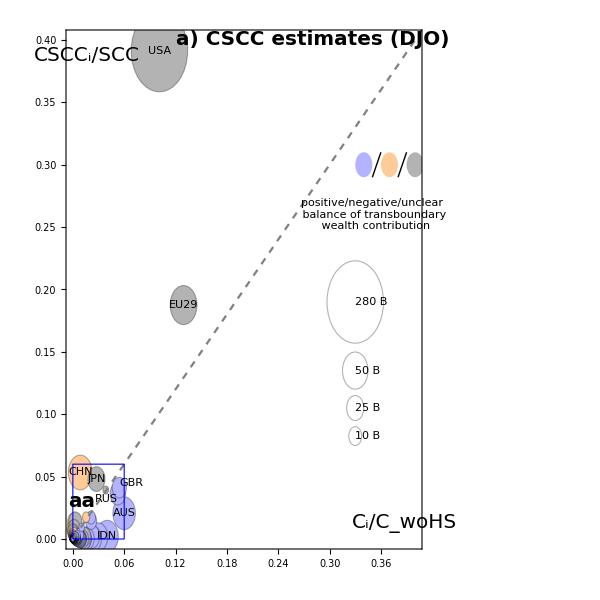

```mathematica
p1a=Show[BubbleChart[sdatDJOr[[;;,{9,3,12}]], PlotRange->{{0,0.4},{0, 0.4}}, BubbleSizes->{0.01,0.2},ChartStyle->sdatDJOr[[;;,16]],Axes->True, AxesOrigin->{0,0},BaseStyle->Directive[FontFamily->"Helvetica",FontSize->16,Black],LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16,Black],Frame->True,PerformanceGoal->"Speed",Epilog->{Text[Style[ya,{FontFamily->"Helvetica",FontSize->20}],Offset[{0,0},Scaled[{0.06,0.95}]],{0,0}],Text[Style[xa,{FontFamily->"Helvetica",FontSize->20}],Offset[{0,0},Scaled[{0.95,0.05}]],{0,0}]},ImageSize->600],Plot[x,{x,0,0.5},PlotStyle->{Gray, Dashed}],Graphics[labDJOb[[;;,2]]],djoL,snip,Graphics[Text["positive/negative/unclear \n balance of transboundary \n wealth contribution",{0.352,0.26}]],Graphics[Text[Style["a) CSCC estimates (DJO)",FontSize->20,Bold],{0.28,0.4}]],Graphics[Text[Style["aa",FontSize->20,Bold],{0.01,0.03}]]]
```

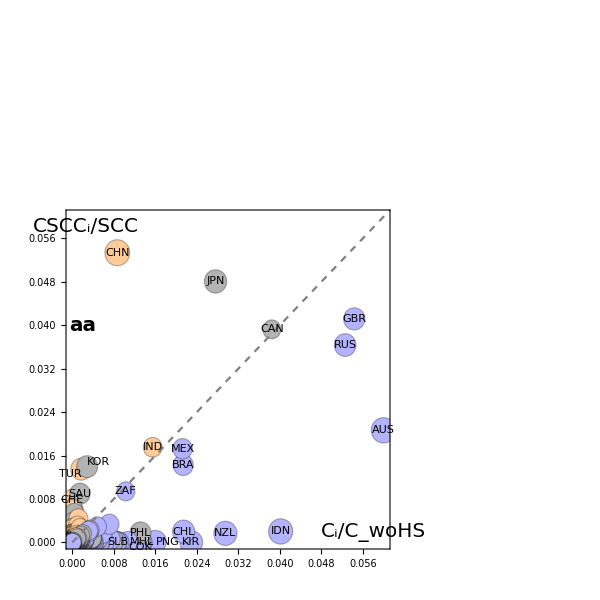

```mathematica
p1aa=Show[BubbleChart[sdatDJOr[[;;,{9,3,12}]], PlotRange->{{0,0.06},{0, 0.06}}, BubbleSizes->{0.01,0.15288720651615714*0.14},ChartStyle->sdatDJOr[[;;,16]],BaseStyle->Directive[FontFamily->"Helvetica",FontSize->16,Black],LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16,Black],Frame->True,PerformanceGoal->"Speed",Epilog->{Text[Style[ya,{FontFamily->"Helvetica",FontSize->20}],Offset[{0,0},Scaled[{0.06,0.95}]],{0,0}],Text[Style[xa,{FontFamily->"Helvetica",FontSize->20}],Offset[{0,0},Scaled[{0.95,0.05}]],{0,0}]},ImageSize->600],Plot[x,{x,0,0.4},PlotStyle->{Gray, Dashed}],Graphics[labDJOs[[;;,2]]],Graphics[Text[Style["aa",FontSize->20,Bold],{0.002,0.04}]]]
```

```mathematica
sdatTol=SortBy[datTol[[2;;]],{#[[13]]&}];
Do[sdatTol[[i,14]]=i,{i,1,165}];
Do[If[sdatTol[[i,3]]>0.0075 ∨sdatTol[[i,9]]>0.01 , sdatTol[[i,15]]=sdatTol[[i,14]]],{i,1,165}]
rT={{"30 B",0,0.19,0,0,0,0,0,0.33,0,0,30000.0,0,0,0,White},{"15 B",0,0.165,0,0,0,0,0,0.33,0,0,15000.0,0,0,0,White},{"10 B",0,0.145,0,0,0,0,0,0.33,0,0,10000.0,0,0,0,White},{"  5 B",0,0.125,0,0,0,0,0,0.33,0,0,5000.0,0,0,0,White}};
datTolr=Join[datTol,rT];
sdatTolr=Join[sdatTol,rT];
```

```mathematica
setTol={1,2,3,4,166,167,168,169};
labTolb=Table[{coorTL={sdatTolr[[setTol[[i]],9]],sdatTolr[[setTol[[i]],3]]},Text[sdatTolr[[setTol[[i]],1]],coorTL,{0,-2}]},{i,1,Dimensions[setTol][[1]]}];
labTolb[[1,2,3]]={0,-3};
Do[labTolb[[i,2,3]]={-2.5,0},{i,5,8}];
ssetT=DeleteCases[sdatTol[[;;,15]],0];
labTols=Table[{coorTs={sdatTol[[ssetT[[i]],9]],sdatTol[[ssetT[[i]],3]]},Text[sdatTol[[ssetT[[i]],1]],coorTs,{0,-1.5}]},{i,1,Dimensions[ssetT][[1]]}];
tempTol=Table[0,{i,1,37}];
Do[tempTol[[i]]=sdatTol[[ssetT[[i]],1]],{i,1,37}]
```

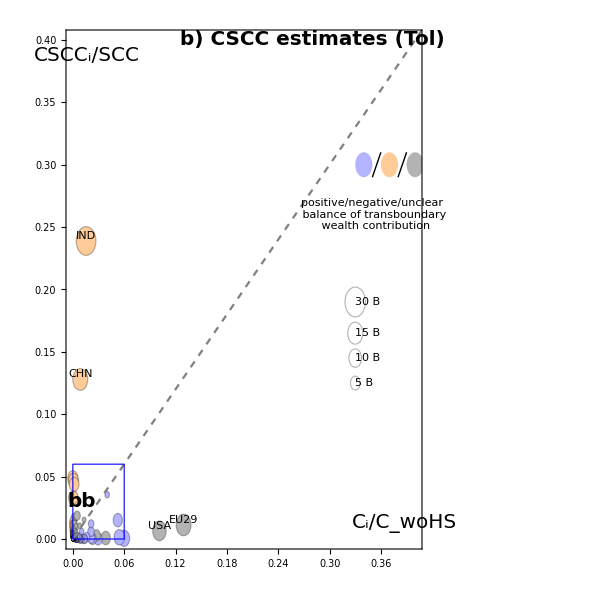

```mathematica
p1b=Show[BubbleChart[sdatTolr[[;;,{9,3,12}]], PlotRange->{{0,0.4},{0, 0.4}}, BubbleSizes->{0.01,0.1},ChartStyle->sdatTolr[[;;,16]],Axes->True, AxesOrigin->{0,0},BaseStyle->Directive[FontFamily->"Helvetica",FontSize->16,Black],LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16,Black],Frame->True,PerformanceGoal->"Speed",Epilog->{Text[Style[ya,{FontFamily->"Helvetica",FontSize->20}],Offset[{0,0},Scaled[{0.06,0.95}]],{0,0}],Text[Style[xa,{FontFamily->"Helvetica",FontSize->20}],Offset[{0,0},Scaled[{0.95,0.05}]],{0,0}]},ImageSize->600],Plot[x,{x,0,0.5},PlotStyle->{Gray, Dashed}],Graphics[labTolb[[;;,2]]],djoL,snip,Graphics[Text["positive/negative/unclear \n balance of transboundary \n wealth contribution",{0.352,0.26}]],Graphics[Text[Style["b) CSCC estimates (Tol)",FontSize->20,Bold],{0.28,0.4}]],Graphics[Text[Style["bb",FontSize->20,Bold],{0.01,0.03}]]]
```

```mathematica
labTols[[13,2,3]]={-0.5,1.5};
labTols[[16,2,3]]={-0.5,1.5};
labTols[[24,2,3]]={0,1.5};
labTols[[27,2,3]]={0,0};
labTols[[25,2,3]]={-1,-0.5};(*KEN*)
labTols[[26,2,3]]={0.6,-1.2};(*AFG*)
labTols[[28,2,3]]={0,-0.7};
labTols[[29,2,3]]={-1,0};
labTols[[31,2,3]]={0,-0.7};(*MWI*)
labTols[[32,2,3]]={0,0.2};(*NER*)
labTols[[33,2,3]]={-0.3,-0.8}(*MOZ*)
```

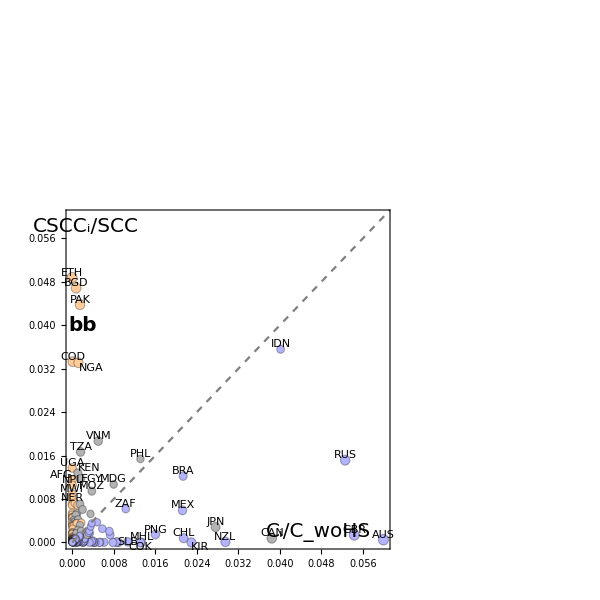

```mathematica
p1bb=Show[BubbleChart[sdatTol[[;;,{9,3,12}]], PlotRange->{{0,0.06},{0, 0.06}},BubbleSizes->{0.01,0.02}, ChartStyle->sdatTol[[;;,16]],Axes->True, AxesOrigin->{0,0},BaseStyle->Directive[FontFamily->"Helvetica",FontSize->16,Black],LabelStyle->Directive[FontFamily->"Helvetica",FontSize->16,Black],Frame->True,PerformanceGoal->"Speed",Epilog->{Text[Style[ya,{FontFamily->"Helvetica",FontSize->20}],Offset[{0,0},Scaled[{0.06,0.95}]],{0,0}],Text[Style[xa,{FontFamily->"Helvetica",FontSize->20}],Offset[{0,0},Scaled[{0.78,0.05}]],{0,0}]}, ImageSize->600],Plot[x,{x,0,0.4},PlotStyle->{Gray, Dashed}],Graphics[labTols[[;;,2]]],Graphics[Text[Style["bb",FontSize->20,Bold],{0.002,0.04}]]]
```

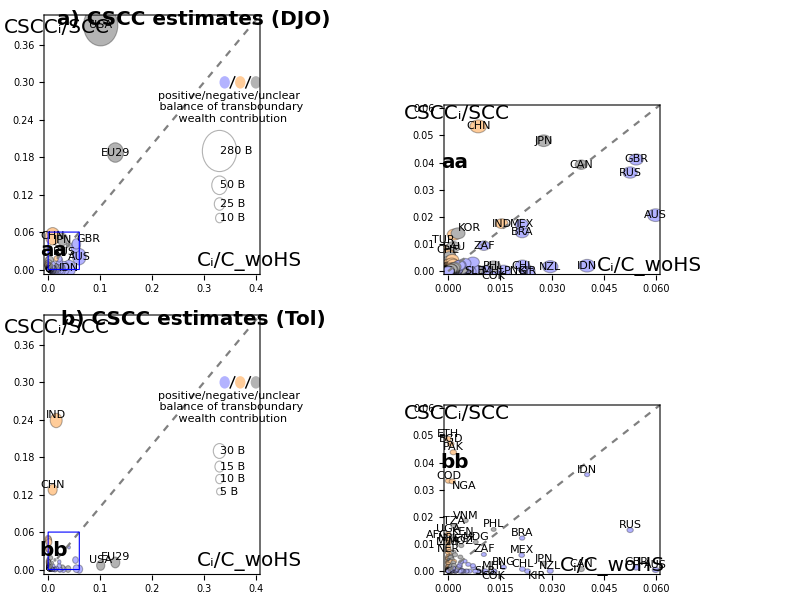

```mathematica
Fig3=Grid[{{p1a,p1aa},{p1b,p1bb}},Frame->True]
```

```mathematica
(*Export["Figure_3.pdf",Fig3,ImageResolution->400]*)
```

```mathematica
fSF3data=Import["Data_Figure_SMF3.csv"];
```

```mathematica
test=Import["F5_SinkReduc_data.csv"];
```

```mathematica
Dimensions[test]
Dimensions[fSF3data]
```

{32,28}

{32,28}

```mathematica
fSF3dat=Table[0,{i,29},{j,5}];
fSF3dat[[1]]={"sink_red","cno_trade","ctrade","pno_trade","ptrade"};
fSF3dat[[2;;,1]]=fSF3data[[2;;29,1]];
fSF3dat[[2,1]]=0;
fSF3dat[[2;;,1]]=fSF3data[[2;;29,1]]*100;
Do[fSF3dat[[i,2]]=Around[fSF3data[[i,16]],fSF3data[[i,17]]],{i,2,29}]
Do[fSF3dat[[i,3]]=Around[fSF3data[[i,22]],fSF3data[[i,23]]],{i,2,29}]
Do[fSF3dat[[i,5]]=Around[fSF3data[[i,6]],fSF3data[[i,7]]],{i,2,29}]
Do[fSF3dat[[i,4]]=Around[fSF3data[[i,11]],fSF3data[[i,12]]],{i,2,29}]
```

```mathematica
FigSF3a=ListLinePlot[{fSF3dat[[2;;,{1,2}]],fSF3dat[[2;;,{1,3}]]},IntervalMarkers->"Bands",PlotStyle->{{Magenta,Thick} ,{Orange,Thick}},IntervalMarkersStyle->{Lighter[Magenta,0.7],Lighter[Orange,0.7]}, PlotRange->{{0,10},{0,400}},Frame->{True,True,False,False},FrameLabel->{"Decrease ocean sink in percent","Aggregated Cost in B USD (2020)",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],Epilog->{Text[Style["a",{FontFamily->"Helvetica",Bold,FontSize->14,TextAlignment->Right}],Offset[{0,0},Scaled[{0.05,0.97}]],{0,0}]},ImageSize->400];
```

```mathematica
f5b=ListLinePlot[{fSF3dat[[2;;,{1,4}]],fSF3dat[[2;;,{1,5}]]},IntervalMarkers->"Bands",PlotStyle->{{Magenta,Thick} ,{Orange,Thick}},IntervalMarkersStyle->{Lighter[Magenta,0.7],Lighter[Orange,0.7]}, PlotRange->{{0,10},{0,80}},Frame->{True,True,False,False},FrameLabel->{"Decrease ocean sink in percent","CO_2 price USD/tCO_2",None,None},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],Epilog->{Text[Style["b",{FontFamily->"Helvetica",Bold,FontSize->14,TextAlignment->Right}],Offset[{0,0},Scaled[{0.05,0.97}]],{0,0}]},ImageSize->400];
```

```mathematica
LineLegend[{{Magenta,AbsoluteThickness[3]},{Orange,AbsoluteThickness[3]},Black},{Style["no emissions trading",FontFamily->"Helvetica",FontSize->14],Style["full emissions trading",FontFamily->"Helvetica",FontSize->14]},LegendLayout->{"Row",1}]
```

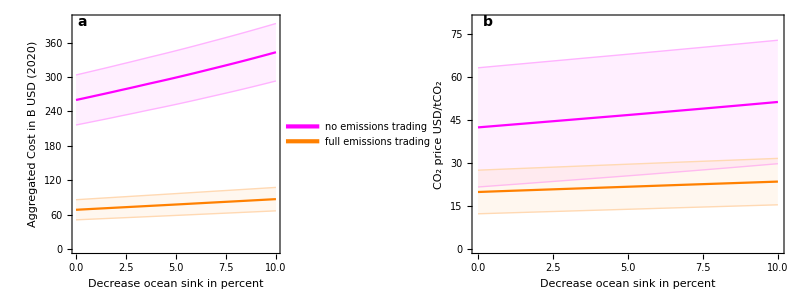

```mathematica
fig5=Legended[Grid[{{f5a,f5b}},Frame->All],Placed[LineLegend[{{Magenta,AbsoluteThickness[3]},{Orange,AbsoluteThickness[3]},Black},{Style["no emissions trading",FontFamily->"Helvetica",FontSize->14],Style["full emissions trading",FontFamily->"Helvetica",FontSize->14]},LegendLayout->{"Row",1}],Below]]
```

```mathematica
(*Export["fig5.png",fig5,ImageResolution->400]
Export["Figure_SMF3.pdf",fig5,ImageResolution->400]*)
```